# KASUS TOV GR constant energy density

## Backward lalu Forward

### Backward calculation

```mathematica
Clear["Global`*"]
```

```mathematica
B=60.
ϵ[p_]=0 p+4B (* Model Quark Star *)
dϵdp=D[ϵ[p],p];
```

60.

240.

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
```

```mathematica
rmax0=10^(-3);
M=MSS*2.61; (* Massa di permukaan *)
k=0.541276549838625;
R=(2 GS M)/k;(* radius di permukaan *)
PCC=1.*^-15; (* Tekanan di permukaan *)

r00=R;
MCC=M;
(*NumberForm[{r00,R},20]
NumberForm[{(MCC/MSS),(M/MSS)},20]*)

Clear[rStar2];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r00]==MCC , p[r00]==PCC},{m,p},{r,r00,rmax0},Method->{"EventLocator","Event" :>{r-1.0001 2GS m[r]},"EventAction":>Throw[rStar2=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax0]
solb=NDSolve`ProcessSolutions[state]

moo[r_]=Evaluate[m[r]/. solb];
poo[r_]=Evaluate[p[r]/. solb];

NumberForm[poo'[rmax0],12]
```

{m→InterpolatingFunction[{{0.001, 14254.}}, <>],p→InterpolatingFunction[{{0.001, 14254.}}, <>]}

0.0393453680809

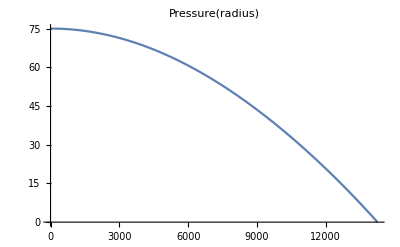

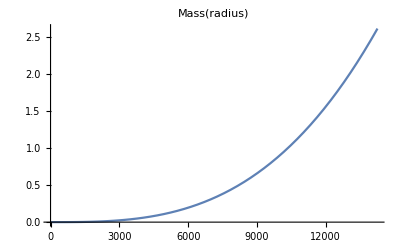

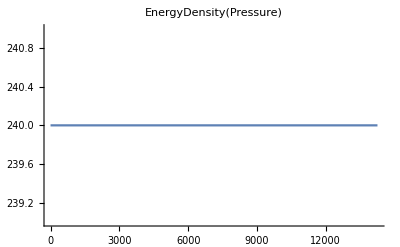

```mathematica
mStar=moo[rStar];
Plot[{poo[r]},{r,rmax0,r00},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{moo[r]/MSS},{r,rmax0,r00},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[poo[r]]},{r,rmax0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

```mathematica
{rmax0,poo[rmax0],moo[rmax0]/MSS}
{r00,moo[r00]/MSS,poo[r00]}
```

{1/1000,75.0577,-8.44925×10^-14}

{14254.,2.61,1.×10^-15}

### Reverse calculation

```mathematica
r0=rmax0;(* radius di pusat *)
rmax=100000.;
MCC=moo[rmax0]; (* Massa di pusat *)
PCC=poo[rmax0]; (* Tekanan di pusat *)
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
solf=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 14254.}}, <>],p→InterpolatingFunction[{{0.001, 14254.}}, <>]}

14254.

```mathematica
mo[r_]=Evaluate[m[r]/. solf];
po[r_]=Evaluate[p[r]/. solf];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

14253.999441525391     2.6099998884601674     240.     75.0577

-Graphics-

-Graphics-

-Graphics-

```mathematica
{r0,po[r0],mo[r0]/MSS}
{rStar,mo[rStar]/MSS,po[rStar]}
```

{1/1000,75.0577,-8.44925×10^-14}

{14254.,2.61,6.30052×10^-15}

### Perbandingan

```mathematica
(* backward *) 

NumberForm[{rmax0,moo[rmax0]/MSS,poo[rmax0]},12]
NumberForm[{r00,moo[r00]/MSS,poo[r00]},12]
```

{1/1000,-8.44925071539×10^-14,75.0576833754}

{14253.9996464,2.61,1.×10^-15}

```mathematica
(* forward *) 

NumberForm[{r0,mo[r0]/MSS,po[r0]},12]
NumberForm[{rStar,mo[rStar]/MSS,po[rStar]},12]
```

{1/1000,-8.44925071539×10^-14,75.0576833754}

{14253.9994415,2.60999988846,6.30051566475×10^-15}

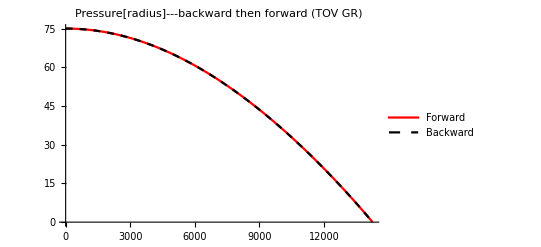

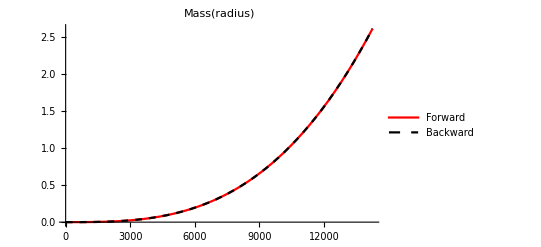

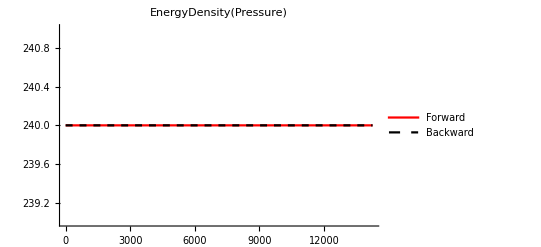

```mathematica
Plot[{po[r],poo[r]},{r,r0,r00},PlotRange->All,PlotLabel->"Pressure[radius]---backward then forward (TOV GR)",PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{mo[r]/MSS,moo[r]/MSS},{r,r0,r00},PlotRange->All,PlotLabel->Mass[radius],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
Plot[{ϵ[po[r]],ϵ[poo[r]]},{r,r0,r00},PlotRange->All,PlotLabel->EnergyDensity[Pressure],PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Forward","Backward"}]
```

Keluarin datanya

```mathematica
ClearAll[x,data]
x[i_]:=r0+i(r00-r0)/1000
data:=Table[{x[i]/1000,poo[x[i]],po[x[i]],moo[x[i]]/MSS,mo[x[i]]/MSS,ϵ[poo[x[i]]],ϵ[po[x[i]]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-4.1.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-4.1.dat